## Import Utils

```mathematica
Get["D:\\Documents\\workspace\\课题\\workspace\\Local\\Public\\mathematica\\PN_inverse\\InversePNUtils.nb"];
```

```mathematica
(*NotebookEvaluate["D:\\Documents\\workspace\\课题\\PN_inverse\\InversePNUtils.nb"]*)
```

```mathematica
NotebookEvaluate["D:\\Documents\\workspace\\课题\\workspace\\Local\\Public\\mathematica\\PN_inverse\\InversePNUtils.nb"];
```

输入Mc范围：{8,15}

输入q范围：{1,20}

m1范围：{9.18959,91.4002}

m2范围：{2.43734,17.2305}

输入Mc范围：{6,13}

输入q范围：{1,7}

m1范围：{6.89219,42.9142}

m2范围：{2.8295,14.9331}

全局极小值结果：{0.,{m1→3.,m2→3.,spin1z→0.99,spin2z→0.99}}

全局极大值结果：{0.,{m1→3.,m2→3.,spin1z→0.99,spin2z→0.99}}

全局极小值结果：{2.81559×10^-11,{m1→46.8969,m2→60.4341,spin1z→0.435746,spin2z→-0.638885}}

全局极大值结果：{8.65708,{m1→100.,m2→3.,spin1z→0.99,spin2z→0.99}}

全局极小值结果：{8.47209×10^-10,{m1→60.1419,m2→76.87,spin1z→0.320417,spin2z→-0.443897}}

全局极大值结果：{1.94773,{m1→100.,m2→3.,spin1z→0.99,spin2z→0.99}}

### Read from CSV

```mathematica
(* ==================配置==================*)
baseDir="D:\\Documents\\workspace\\课题\\workspace\\Local\\Parameterized_PN_Tests\\csv";
eventID="GW150914";

(*键名直接用短名，里面加上下划线*)
inspiralParams={"dphi_0","dphi_2","dphi_3","dphi_4","dphi_5l","dphi_6","dphi_6l","dphi_7"};
intermediateParams={"dbeta_2","dbeta_3"};
mergerParams={"dalpha_2","dalpha_3","dalpha_4"};

allParams=Join[inspiralParams,intermediateParams,mergerParams];

(* ==================读取函数==================*)
readDeviationFile[shortName_]:=Module[{path,raw},(*短名拼接上 _IMRP_posterior 还原成完整文件名*)path=FileNameJoin[{baseDir,eventID,shortName<>"_IMRP_posterior.csv"}];
raw=Import[path];
(*提取前五列*){raw[[2;;,1]],(*m1*)raw[[2;;,2]],(*m2*)raw[[2;;,3]],(*spin1z*)raw[[2;;,4]],(*spin2z*)raw[[2;;,5]]  (*偏差参数值*)}]

(*批量读取，键名就是传入的 shortName*)
readAllDeviations[]:=AssociationMap[readDeviationFile,allParams]

(* ==================执行==================*)
samples=readAllDeviations[];

(* ==================用法示例==================*)
(*直接用短名取值*)
dphi0vals=samples["dphi_0"][[5]];
dalpha3vals=samples["dalpha_3"][[5]];
```

## Calculate GR pars and further Transform $\delta$ into parameterized pars

```mathematica
(*批量计算非自旋 GR 系数值*)getGRValues[paramName_,m1s_,m2s_,chi1Ls_,chi2Ls_]:=Module[{etas},etas=etaFromMasses[m1s,m2s];
Switch[paramName,
(* =====Alpha (并合段)=====*)
"dalpha_2",IMRPhenomDAlpha[2,m1s,m2s,chi1Ls,chi2Ls],
"dalpha_3",IMRPhenomDAlpha[3,m1s,m2s,chi1Ls,chi2Ls],
"dalpha_4",IMRPhenomDAlpha[4,m1s,m2s,chi1Ls,chi2Ls],
(* =====Beta (过渡段)=====*)
"dbeta_2",IMRPhenomDBeta[2,m1s,m2s,chi1Ls,chi2Ls],
"dbeta_3",IMRPhenomDBeta[3,m1s,m2s,chi1Ls,chi2Ls],
(* =====Phi (旋近段)=====因为设置了 Listable，直接把整个 m1s,m2s 列表传进去即可，内部会自动对每个元素计算并返回列表*)
"dphi_0",IMRPhenomDPhiNS[0,m1s,m2s,0,0],
"dphi_2",IMRPhenomDPhiNS[2,m1s,m2s,0,0],
"dphi_3",IMRPhenomDPhiNS[3,m1s,m2s,0,0],
"dphi_4",IMRPhenomDPhiNS[4,m1s,m2s,0,0],
"dphi_5l",IMRPhenomDPhiLNS[5,m1s,m2s,0,0],
"dphi_6",IMRPhenomDPhiNS[6,m1s,m2s,0,0],
"dphi_6l",IMRPhenomDPhiLNS[6,m1s,m2s,0,0],
"dphi_7",IMRPhenomDPhiNS[7,m1s,m2s,0,0],
_,ConstantArray[0,Length[m1s]]
]
];

(* ==========对所有参数追加第6列(GR值)和第7列(参数化值)==========*)
Do[Module[{grVals,paramVals},
(*第6列：非自旋 GR 系数值*)grVals=getGRValues[p,samples[p][[1]],samples[p][[2]],samples[p][[3]],samples[p][[4]]];
(*第7列：参数化值=GR×(1+d)*)paramVals=grVals*(1+samples[p][[5]]);
(*拼接到原来的5列后面*)samples[p]=Join[samples[p],{grVals,paramVals}];
],{p,allParams}];
```

```mathematica
samples["dalpha_3"][[6]]
```

```mathematica
CalculateSampleRatios[samples,{35.5,29.9},{35.5-3.1,29.9-4.5},{35.5+5.1,29.9+3.0}]
```

{<|p→dphi_0,LowerBoundRatios→<|1→1.05627,2→0.841538|>,MedianRatios→<|1→1.0885,2→0.994134|>,UpperBoundRatios→<|1→1.09104,2→1.06441|>,WidthRatios→<|1→1.22842,2→1.81918|>|>,<|p→dphi_2,LowerBoundRatios→<|1→1.04185,2→0.827033|>,MedianRatios→<|1→1.09698,2→0.958047|>,UpperBoundRatios→<|1→1.09844,2→1.04686|>,WidthRatios→<|1→1.32205,2→1.79133|>|>,<|p→dphi_3,LowerBoundRatios→<|1→1.03444,2→0.844279|>,MedianRatios→<|1→1.07575,2→0.982997|>,UpperBoundRatios→<|1→1.08597,2→1.04639|>,WidthRatios→<|1→1.28956,2→1.73087|>|>,<|p→dphi_4,LowerBoundRatios→<|1→1.04008,2→0.822671|>,MedianRatios→<|1→1.10338,2→0.951138|>,UpperBoundRatios→<|1→1.10638,2→1.04022|>,WidthRatios→<|1→1.36831,2→1.77698|>|>,<|p→dphi_5l,LowerBoundRatios→<|1→1.04654,2→0.846059|>,MedianRatios→<|1→1.09595,2→0.96028|>,UpperBoundRatios→<|1→1.0979,2→1.035|>,WidthRatios→<|1→1.30082,2→1.6749|>|>,<|p→dphi_6,LowerBoundRatios→<|1→1.04267,2→0.901142|>,MedianRatios→<|1→1.07958,2→0.987286|>,UpperBoundRatios→<|1→1.08485,2→1.04476|>,WidthRatios→<|1→1.25151,2→1.53115|>|>,<|p→dphi_6l,LowerBoundRatios→<|1→1.03872,2→0.868742|>,MedianRatios→<|1→1.08513,2→0.977471|>,UpperBoundRatios→<|1→1.07935,2→1.04093|>,WidthRatios→<|1→1.23988,2→1.62406|>|>,<|p→dphi_7,LowerBoundRatios→<|1→1.04554,2→0.918951|>,MedianRatios→<|1→1.075,2→0.993093|>,UpperBoundRatios→<|1→1.08226,2→1.04587|>,WidthRatios→<|1→1.22736,2→1.47568|>|>,<|p→dbeta_2,LowerBoundRatios→<|1→1.05685,2→1.07254|>,MedianRatios→<|1→1.0812,2→1.08786|>,UpperBoundRatios→<|1→1.09388,2→1.10174|>,WidthRatios→<|1→1.24023,2→1.20062|>|>,<|p→dbeta_3,LowerBoundRatios→<|1→1.07938,2→1.12354|>,MedianRatios→<|1→1.08037,2→1.10386|>,UpperBoundRatios→<|1→1.09234,2→1.09511|>,WidthRatios→<|1→1.14353,2→0.998824|>|>,<|p→dalpha_2,LowerBoundRatios→<|1→1.07955,2→1.11261|>,MedianRatios→<|1→1.09623,2→1.11124|>,UpperBoundRatios→<|1→1.10693,2→1.12654|>,WidthRatios→<|1→1.21513,2→1.17373|>|>,<|p→dalpha_3,LowerBoundRatios→<|1→1.08645,2→1.10113|>,MedianRatios→<|1→1.09462,2→1.09464|>,UpperBoundRatios→<|1→1.09458,2→1.10867|>,WidthRatios→<|1→1.12669,2→1.13419|>|>,<|p→dalpha_4,LowerBoundRatios→<|1→1.08955,2→1.12267|>,MedianRatios→<|1→1.087,2→1.10553|>,UpperBoundRatios→<|1→1.0803,2→1.10872|>,WidthRatios→<|1→1.04375,2→1.06148|>|>}

## m1-m2 Plot, 22

```mathematica
plots=<||>;
compPlots=<||>;
```

## INSPIRAL

### phi_2

```mathematica
(* ==========================================*)(*阶段一：预处理（算概率、提取红线）*)(* ==========================================*)
p="dphi_2"; (*换参数改这里*)

m1Data=samples[p][[1]];
m2Data=samples[p][[2]];

(*算 PDF*)
m1m2[p]=Transpose[{m1Data,m2Data}];
{m1PriorRange[p],m2PriorRange[p]}=ChirpQRangeToMassRange[{10,80},{1,5}];
m1m2PDF[p]=GetNormalizedPDF[m1m2[p],m1PriorRange[p],m2PriorRange[p]];

(*提取 0.005 密度对应的红线*)
contourPD[p]={0.00101};
{contourPlotObj[p],contourPoints[p]}=GetContourPlotAndPoints[m1m2PDF[p],m1PriorRange[p],m2PriorRange[p],contourPD[p]];
contourPoints[p][[1]]=SmoothContour[contourPoints[p][[1]]];

(*算出红线内部包含的真实后验概率 prob*)
prob=CalculateCredibleLevelsFromContours[m1m2PDF[p],{mergeSymmetricCurves[contourPoints[p][[1]],contourPoints[p][[2]]]},"",False][[1]][[2]];

Print[p," 预处理完成，红线包含概率 prob = ",prob];
```

输入Mc范围：{10,80}

输入q范围：{1,5}

m1范围：{11.487,217.926}

m2范围：{5.44814,91.8959}

对称数据：原始 17687 + 镜像 17687

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1. and 3.86295×10^-6 for the integral and error estimates.

对称先验空间积分 = 1.（应接近1）

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1. and 3.86295×10^-6 for the integral and error estimates.

归一化验证 = 1.

Set::wrsym: Symbol Automatic is Protected.

对称边界框：{5.44814, 217.926} × {5.44814, 217.926}

等高线值：{0.00101}，共 2 条

第一条前3点：{{27.892,28.556},{27.8389,28.6025},{27.6747,28.7442}}

Set::setps: contourPoints[p] in the part assignment is not a symbol.

NIntegrate::regm: Method LocalAdaptive is not applicable for a region domain. Continuing with method Automatic.

=====  =====

包含片段数：1 (合并模式: False)

区域内总积分值：0.913256

可信水平百分比：91.3256%

==========================

dphi_2 预处理完成，红线包含概率 prob = 0.913256

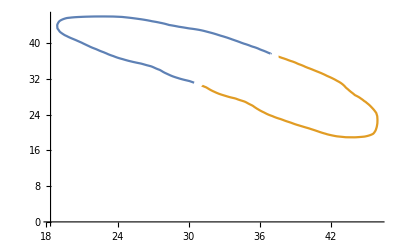

```mathematica
ListLinePlot[contourPoints[p]]
```

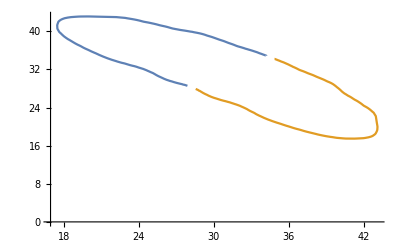

```mathematica
ListLinePlot[contourPoints[p]]
```

```mathematica
compPlots[p]=PlotComparisonBetween[samples[p][[7]],(*第7列：参数化系数样本*)samples[p][[6]],(*第6列：GR理论预测样本*)Range[10,100,1],(*m1 范围*)orderVal,(*阶数 order*)Median[chi1Data],(*自旋1*)Median[chi2Data]           (*自旋2*)]
```

====== [dphi_2] 反解校验报告 (容差: 1/100000) ======

实际使用的概率区间上下界: {0.0111, 0.9889}

实际使用的 GR 概率区间上下界: {6.18422, 6.44178}

实际使用的 Param 概率区间上下界: {6.44104, 12.4944}

GR下界: 点数=500 | Y>0点数=500 | 平均误差=2.93099×10^-16

GR上界: 点数=500 | Y>0点数=500 | 平均误差=1.93623×10^-16

Param下界: 点数=500 | Y>0点数=500 | 平均误差=9.62785×10^-16

Param上界: 点数=500 | Y>0点数=500 | 平均误差=6.05257

{{10.1,9.6594},{10.2,9.75503},{10.3,9.85067},{10.4,9.94631},{10.5,10.0419}}

{{10.1,10.1},{10.2,10.2003},{10.3,10.2993},{10.4,10.3999},{10.5,10.5}}

chi1L取值：0.0841369

chi2L取值：0.258801

=====================================================

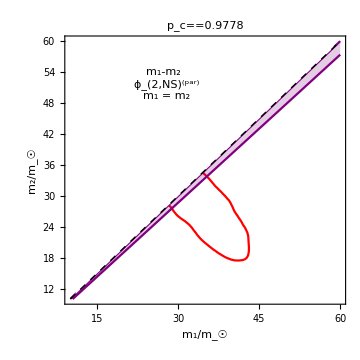

```mathematica
probability=prob;
probability=0.8925058374665041;
probability=0.9778;

plots[p]=PlotInversion[p,probability,10,60,0.1,cm->True,cd->False,cu->False,plotgr->False,projX->False,projY->False,funcName->IMRPhenomDPhiNS,spinPercentile1->0.5,spinPercentile2->0.5,contourIndices->{1,2},m1m2region->{mergeSymmetricCurves[contourPoints[p][[1]],contourPoints[p][[2]],2]}]
```

### phi_4

```mathematica
(* ==========================================*)(*阶段一：预处理（算概率、提取红线）*)(* ==========================================*)
p="dphi_4"; (*换参数改这里*)

m1Data=samples[p][[1]];
m2Data=samples[p][[2]];

(*算 PDF*)
m1m2[p]=Transpose[{m1Data,m2Data}];
{m1PriorRange[p],m2PriorRange[p]}=ChirpQRangeToMassRange[{10,80},{1,5}];
m1m2PDF[p]=GetNormalizedPDF[m1m2[p],m1PriorRange[p],m2PriorRange[p]];

(*提取 0.005 密度对应的红线*)
contourPD[p]={0.000783};
{contourPlotObj[p],contourPoints[p]}=GetContourPlotAndPoints[m1m2PDF[p],m1PriorRange[p],m2PriorRange[p],contourPD[p]];
contourPoints[p][[1]]=SmoothContour[contourPoints[p][[1]]];

(*算出红线内部包含的真实后验概率 prob*)
prob=CalculateCredibleLevelsFromContours[m1m2PDF[p],{mergeSymmetricCurves[contourPoints[p][[1]],contourPoints[p][[2]]]},"",False][[1]][[2]];

Print[p," 预处理完成，红线包含概率 prob = ",prob];
```

输入Mc范围：{10,80}

输入q范围：{1,5}

m1范围：{11.487,217.926}

m2范围：{5.44814,91.8959}

对称数据：原始 16389 + 镜像 16389

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1. and 4.20691×10^-6 for the integral and error estimates.

对称先验空间积分 = 1.（应接近1）

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1. and 4.20691×10^-6 for the integral and error estimates.

归一化验证 = 1.

Set::wrsym: Symbol Automatic is Protected.

对称边界框：{5.44814, 217.926} × {5.44814, 217.926}

等高线值：{0.000783}，共 2 条

第一条前3点：{{27.3293,27.9924},{27.3286,27.9926},{27.1997,28.1913}}

Set::setps: contourPoints[p] in the part assignment is not a symbol.

NIntegrate::regm: Method LocalAdaptive is not applicable for a region domain. Continuing with method Automatic.

=====  =====

包含片段数：1 (合并模式: False)

区域内总积分值：0.932936

可信水平百分比：93.2936%

==========================

dphi_4 预处理完成，红线包含概率 prob = 0.932936

```mathematica
p="dphi_4"; 
compPlots[p]=PlotComparisonBetween[samples[p][[7]],(*第7列：参数化系数样本*)samples[p][[6]],(*第6列：GR理论预测样本*)Range[10,100,1],(*m1 范围*)orderVal,(*阶数 order*)Median[chi1Data],(*自旋1*)Median[chi2Data]           (*自旋2*)]
```

```mathematica
prob
```

0.923761

====== [dphi_4] 反解校验报告 (容差: 1/100000) ======

实际使用的概率区间上下界: {0.4, 0.6}

实际使用的 GR 概率区间上下界: {45.5563, 45.9634}

实际使用的 Param 概率区间上下界: {60.056, 65.99}

GR下界: 点数=500 | Y>0点数=500 | 平均误差=5.88329×10^-15

GR上界: 点数=500 | Y>0点数=500 | 平均误差=6.807×10^-15

Param下界: 点数=500 | Y>0点数=0 | 平均误差=3.68203×10^-14

Param上界: 点数=500 | Y>0点数=500 | 平均误差=19.7441

{{10.1,-4.74832},{10.2,-4.79533},{10.3,-4.84234},{10.4,-4.88936},{10.5,-4.93637}}

{{10.1,10.1001},{10.2,10.2},{10.3,10.3002},{10.4,10.3998},{10.5,10.5001}}

chi1L取值：0.0848845

chi2L取值：0.262031

=====================================================

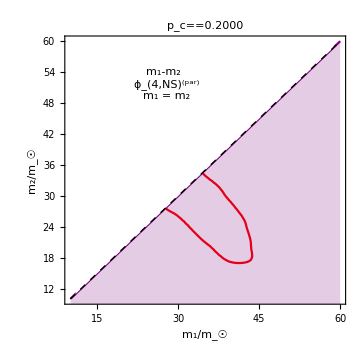

```mathematica
probability=prob;
(*probability=0.9237609941746582;*)
(*probability=0.535;*)
probability=0.2;

plots[p]=PlotInversion[p,probability,10,60,0.1,cm->True,cd->False,cu->False,plotgr->False,projX->False,projY->False,funcName->IMRPhenomDPhiNS,spinPercentile1->0.5,spinPercentile2->0.5,contourIndices->{1,2},m1m2region->{mergeSymmetricCurves[contourPoints[p][[1]],contourPoints[p][[2]],2]}]
```

====== [dphi_4] 反解校验报告 (容差: 1/100000) ======

实际使用的概率区间上下界: {0.07825, 0.92175}

实际使用的 GR 概率区间上下界: {44.2361, 46.2351}

实际使用的 Param 概率区间上下界: {48.7096, 81.6742}

GR下界: 点数=300 | Y>0点数=300 | 平均误差=4.54747×10^-15

GR上界: 点数=300 | Y>0点数=300 | 平均误差=1.56319×10^-15

Param下界: 点数=300 | Y>0点数=300 | 平均误差=2.46368

Param上界: 点数=300 | Y>0点数=300 | 平均误差=35.4283

{{20.1,20.1},{20.2,20.2},{20.3,20.3},{20.4,20.4},{20.5,20.5}}

{{20.1,20.0996},{20.2,20.1995},{20.3,20.2993},{20.4,20.3996},{20.5,20.5003}}

chi1L取值：0.0848845

chi2L取值：0.262031

=====================================================

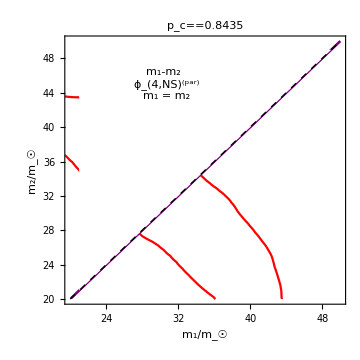

```mathematica
probability=prob;
(*probability=0.9237609941746582;*)
(*probability=0.535;*)
probability=0.8435;

plots[p]=PlotInversion[p,probability,20,50,0.1,cm->True,cd->False,cu->False,plotgr->False,projX->False,projY->False,funcName->IMRPhenomDPhiNS,spinPercentile1->0.5,spinPercentile2->0.5,contourIndices->{1,2},m1m2region->{mergeSymmetricCurves[contourPoints[p][[1]],contourPoints[p][[2]],2]}]
```

### phi_5l

```mathematica
(* ==========================================*)(*阶段一：预处理（算概率、提取红线）*)(* ==========================================*)
p="dphi_5l"; (*换参数改这里*)

m1Data=samples[p][[1]];
m2Data=samples[p][[2]];

(*算 PDF*)
m1m2[p]=Transpose[{m1Data,m2Data}];
{m1PriorRange[p],m2PriorRange[p]}=ChirpQRangeToMassRange[{10,80},{1,5}];
m1m2PDF[p]=GetNormalizedPDF[m1m2[p],m1PriorRange[p],m2PriorRange[p]];

(*提取 0.005 密度对应的红线*)
contourPD[p]={0.00053628};
{contourPlotObj[p],contourPoints[p]}=GetContourPlotAndPoints[m1m2PDF[p],m1PriorRange[p],m2PriorRange[p],contourPD[p]];
contourPoints[p][[1]]=SmoothContour[contourPoints[p][[1]]];

(*算出红线内部包含的真实后验概率 prob*)
prob=CalculateCredibleLevelsFromContours[m1m2PDF[p],{mergeSymmetricCurves[contourPoints[p][[1]],contourPoints[p][[2]]]},"",False][[1]][[2]];

Print[p," 预处理完成，红线包含概率 prob = ",prob];
```

输入Mc范围：{10,80}

输入q范围：{1,5}

m1范围：{11.487,217.926}

m2范围：{5.44814,91.8959}

对称数据：原始 16958 + 镜像 16958

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1. and 4.20934×10^-6 for the integral and error estimates.

对称先验空间积分 = 1.（应接近1）

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1. and 4.20933×10^-6 for the integral and error estimates.

归一化验证 = 1.

Set::wrsym: Symbol Automatic is Protected.

对称边界框：{5.44814, 217.926} × {5.44814, 217.926}

等高线值：{0.00053628}，共 2 条

第一条前3点：{{27.602,28.266},{27.5696,28.293},{27.4446,28.3714}}

Set::setps: contourPoints[p] in the part assignment is not a symbol.

NIntegrate::regm: Method LocalAdaptive is not applicable for a region domain. Continuing with method Automatic.

=====  =====

包含片段数：1 (合并模式: False)

区域内总积分值：0.959771

可信水平百分比：95.9771%

==========================

dphi_5l 预处理完成，红线包含概率 prob = 0.959771

```mathematica
compPlots[p]=PlotComparisonBetween[samples[p][[7]],(*第7列：参数化系数样本*)samples[p][[6]],(*第6列：GR理论预测样本*)Range[10,100,1],(*m1 范围*)orderVal,(*阶数 order*)Median[chi1Data],(*自旋1*)Median[chi2Data]           (*自旋2*)]
```

====== [dphi_5l] 反解校验报告 (容差: 1/100000) ======

实际使用的概率区间上下界: {0.01, 0.99}

实际使用的 GR 概率区间上下界: {464.756, 467.414}

实际使用的 Param 概率区间上下界: {468.682, 916.196}

GR下界: 点数=250 | Y>0点数=250 | 平均误差=6.07088×10^-14

GR上界: 点数=250 | Y>0点数=250 | 平均误差=3.72893×10^-14

Param下界: 点数=250 | Y>0点数=250 | 平均误差=2.63753×10^-14

Param上界: 点数=250 | Y>0点数=250 | 平均误差=434.427

{{10.2,29.0529},{10.4,29.6225},{10.6,30.1922},{10.8,30.7619},{11.,31.3315}}

{{10.2,159778.},{10.4,162911.},{10.6,166044.},{10.8,169177.},{11.,172309.}}

chi1L取值：0.0862003

chi2L取值：0.28772

=====================================================

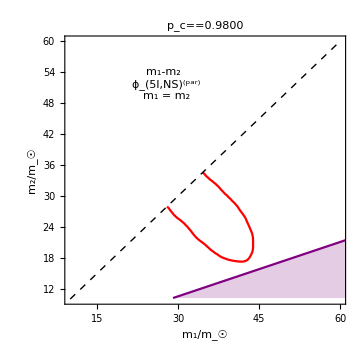

```mathematica
probability=prob;
(*probability=0.9540;
*)
probability=0.98;

plots[p]=PlotInversion[p,probability,10,60,0.2,cm->True,cd->True,cu->True,plotgr->False,projX->False,projY->False,funcName->IMRPhenomDPhiLNS,spinPercentile1->0.5,spinPercentile2->0.5,contourIndices->{1,2},m1m2region->{mergeSymmetricCurves[contourPoints[p][[1]],contourPoints[p][[2]],2]}]
```

### phi_6

```mathematica
(* ==========================================*)(*阶段一：预处理（算概率、提取红线）*)(* ==========================================*)
p="dphi_6"; (*换参数改这里*)

m1Data=samples[p][[1]];
m2Data=samples[p][[2]];

(*算 PDF*)
m1m2[p]=Transpose[{m1Data,m2Data}];
{m1PriorRange[p],m2PriorRange[p]}=ChirpQRangeToMassRange[{10,80}, {1, 10}];
m1m2PDF[p]=GetNormalizedPDF[m1m2[p],m1PriorRange[p],m2PriorRange[p]];

(*提取 0.005 密度对应的红线*)
contourPD[p]={0.00096};
{contourPlotObj[p],contourPoints[p]}=GetContourPlotAndPoints[m1m2PDF[p],m1PriorRange[p],m2PriorRange[p],contourPD[p]];
contourPoints[p][[1]]=SmoothContour[contourPoints[p][[1]]];

(*算出红线内部包含的真实后验概率 prob*)
prob=CalculateCredibleLevelsFromContours[m1m2PDF[p],{mergeSymmetricCurves[contourPoints[p][[1]],contourPoints[p][[2]],2]},"",False][[1]][[2]];

Print[p," 预处理完成，红线包含概率 prob = ",prob];
```

输入Mc范围：{10,80}

输入q范围：{1,10}

m1范围：{11.487,324.615}

m2范围：{4.05769,91.8959}

对称数据：原始 18998 + 镜像 18998

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1. and 2.4254×10^-6 for the integral and error estimates.

对称先验空间积分 = 1.（应接近1）

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1. and 2.4254×10^-6 for the integral and error estimates.

归一化验证 = 1.

Set::wrsym: Symbol Automatic is Protected.

对称边界框：{4.05769, 324.615} × {4.05769, 324.615}

等高线值：{0.00096}，共 2 条

第一条前3点：{{31.3924,30.3933},{31.3925,30.3908},{31.4643,30.339}}

Set::setps: contourPoints[p] in the part assignment is not a symbol.

NIntegrate::regm: Method LocalAdaptive is not applicable for a region domain. Continuing with method Automatic.

=====  =====

包含片段数：1 (合并模式: False)

区域内总积分值：0.922022

可信水平百分比：92.2022%

==========================

dphi_6 预处理完成，红线包含概率 prob = 0.922022

```mathematica
compPlots[p]=PlotComparisonBetween[samples[p][[7]],(*第7列：参数化系数样本*)samples[p][[6]],(*第6列：GR理论预测样本*)Range[10,100,1],(*m1 范围*)orderVal,(*阶数 order*)Median[chi1Data],(*自旋1*)Median[chi2Data]           (*自旋2*)]
```

====== [dphi_6] 反解校验报告 (容差: 1/100000) ======

实际使用的概率区间上下界: {0.038989, 0.961011}

实际使用的 GR 概率区间上下界: {-1104.05, -1021.23}

实际使用的 Param 概率区间上下界: {-996.332, 1395.51}

GR下界: 点数=500 | Y>0点数=500 | 平均误差=1.60526×10^-13

GR上界: 点数=500 | Y>0点数=500 | 平均误差=1.3415×10^-13

Param下界: 点数=500 | Y>0点数=500 | 平均误差=9.77707×10^-14

Param上界: 点数=500 | Y>0点数=500 | 平均误差=1673.78

{{10.1,21.5241},{10.2,21.7373},{10.3,21.9504},{10.4,22.1635},{10.5,22.3766}}

{{10.1,1.99628×10^6},{10.2,2.01605×10^6},{10.3,2.03582×10^6},{10.4,2.05558×10^6},{10.5,2.07535×10^6}}

chi1L取值：0.233562

chi2L取值：0.324994

=====================================================

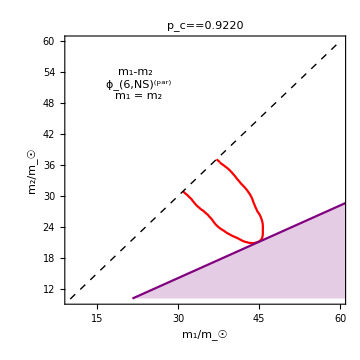

```mathematica
probability=prob;
(*probability=0.9220219417630785;*)

plots[p]=PlotInversion[p,probability,10,60,0.1,cm->True,cd->True,cu->True,plotgr->False,projX->False,projY->False,funcName->IMRPhenomDPhiNS,spinPercentile1->0.5,spinPercentile2->0.5,contourIndices->{1,2},m1m2region->{mergeSymmetricCurves[contourPoints[p][[1]],contourPoints[p][[2]],2]}]
```

### phi_7

```mathematica
(* ==========================================*)(*阶段一：预处理（算概率、提取红线）*)(* ==========================================*)
p="dphi_7"; (*换参数改这里*)

m1Data=samples[p][[1]];
m2Data=samples[p][[2]];

(*算 PDF*)
m1m2[p]=Transpose[{m1Data,m2Data}];
{m1PriorRange[p],m2PriorRange[p]}=ChirpQRangeToMassRange[{10,80}, {1, 8}];
m1m2PDF[p]=GetNormalizedPDF[m1m2[p],m1PriorRange[p],m2PriorRange[p]];

(*提取 0.005 密度对应的红线*)
contourPD[p]={0.000538};
{contourPlotObj[p],contourPoints[p]}=GetContourPlotAndPoints[m1m2PDF[p],m1PriorRange[p],m2PriorRange[p],contourPD[p]];
contourPoints[p][[1]]=SmoothContour[contourPoints[p][[1]]];

(*算出红线内部包含的真实后验概率 prob*)
prob=CalculateCredibleLevelsFromContours[m1m2PDF[p],{mergeSymmetricCurves[contourPoints[p][[1]],contourPoints[p][[2]],2]},"",False][[1]][[2]];

Print[p," 预处理完成，红线包含概率 prob = ",prob];
```

输入Mc范围：{10,80}

输入q范围：{1,8}

m1范围：{11.487,285.216}

m2范围：{4.45651,91.8959}

对称数据：原始 14982 + 镜像 14982

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1. and 4.30183×10^-6 for the integral and error estimates.

对称先验空间积分 = 1.（应接近1）

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1. and 4.30183×10^-6 for the integral and error estimates.

归一化验证 = 1.

Set::wrsym: Symbol Automatic is Protected.

对称边界框：{4.45651, 285.216} × {4.45651, 285.216}

等高线值：{0.000538}，共 2 条

第一条前3点：{{31.4246,30.5472},{31.5559,30.3799},{31.67,30.2567}}

Set::setps: contourPoints[p] in the part assignment is not a symbol.

NIntegrate::regm: Method LocalAdaptive is not applicable for a region domain. Continuing with method Automatic.

=====  =====

包含片段数：1 (合并模式: False)

区域内总积分值：0.956864

可信水平百分比：95.6864%

==========================

dphi_7 预处理完成，红线包含概率 prob = 0.956864

```mathematica
p="dphi_7"; 
compPlots[p]=PlotComparisonBetween[samples[p][[7]],(*第7列：参数化系数样本*)samples[p][[6]],(*第6列：GR理论预测样本*)Range[10,100,1],(*m1 范围*)orderVal,(*阶数 order*)Median[chi1Data],(*自旋1*)Median[chi2Data]           (*自旋2*)]
```

====== [dphi_7] 反解校验报告 (容差: 1/100000) ======

实际使用的概率区间上下界: {0.02155, 0.97845}

实际使用的 GR 概率区间上下界: {1112.45, 1130.89}

实际使用的 Param 概率区间上下界: {1129.34, 8354.33}

GR下界: 点数=250 | Y>0点数=250 | 平均误差=7.63976×10^-14

GR上界: 点数=250 | Y>0点数=250 | 平均误差=3.00133×10^-14

Param下界: 点数=250 | Y>0点数=250 | 平均误差=1.01863×10^-13

Param上界: 点数=250 | Y>0点数=250 | 平均误差=7223.43

{{10.2,8.36332},{10.4,8.52731},{10.6,8.6913},{10.8,8.85528},{11.,9.01927}}

{{10.2,10.205},{10.4,10.3988},{10.6,10.6067},{10.8,10.8074},{11.,10.9925}}

chi1L取值：0.272612

chi2L取值：0.300481

=====================================================

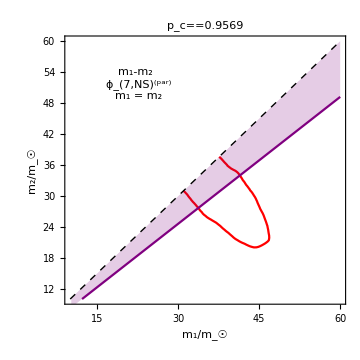

```mathematica
probability=prob;
probability=0.9569;
(*0.32*)
plots[p]=PlotInversion[p,probability,10,60,0.2,cm->True,cd->False,cu->False,plotgr->False,projX->False,projY->False,funcName->IMRPhenomDPhiNS,spinPercentile1->0.5,spinPercentile2->0.5,contourIndices->{1,2},m1m2region->{mergeSymmetricCurves[contourPoints[p][[1]],contourPoints[p][[2]],2]},upStyle->Directive[Purple,Opacity[0]]]
```

## Intermediate

### beta_2

```mathematica
(* ==========================================*)(*阶段一：预处理（算概率、提取红线）*)(* ==========================================*)
p="dbeta_2"; (*换参数改这里*)

m1Data=samples[p][[1]];
m2Data=samples[p][[2]];

(*算 PDF*)
m1m2[p]=Transpose[{m1Data,m2Data}];
{m1PriorRange[p],m2PriorRange[p]}=ChirpQRangeToMassRange[{10,80}, {1, 10}];
m1m2PDF[p]=GetNormalizedPDF[m1m2[p],m1PriorRange[p],m2PriorRange[p]];

(*提取 0.005 密度对应的红线*)
contourPD[p]={0.0015};
{contourPlotObj[p],contourPoints[p]}=GetContourPlotAndPoints[m1m2PDF[p],m1PriorRange[p],m2PriorRange[p],contourPD[p]];
contourPoints[p][[1]]=SmoothContour[contourPoints[p][[1]]];

(*算出红线内部包含的真实后验概率 prob*)
prob=CalculateCredibleLevelsFromContours[m1m2PDF[p],{mergeSymmetricCurves[contourPoints[p][[1]],contourPoints[p][[2]],2]},"",False][[1]][[2]];

Print[p," 预处理完成，红线包含概率 prob = ",prob];
```

输入Mc范围：{10,80}

输入q范围：{1,10}

m1范围：{11.487,324.615}

m2范围：{4.05769,91.8959}

对称数据：原始 21241 + 镜像 21241

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.999997 and 3.87447×10^-6 for the integral and error estimates.

对称先验空间积分 = 0.999997（应接近1）

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1. and 3.87448×10^-6 for the integral and error estimates.

归一化验证 = 1.

Set::wrsym: Symbol Automatic is Protected.

对称边界框：{4.05769, 324.615} × {4.05769, 324.615}

等高线值：{0.0015}，共 2 条

第一条前3点：{{31.5118,32.5135},{31.4815,32.5319},{31.219,32.6943}}

Set::setps: contourPoints[p] in the part assignment is not a symbol.

NIntegrate::regm: Method LocalAdaptive is not applicable for a region domain. Continuing with method Automatic.

=====  =====

包含片段数：1 (合并模式: False)

区域内总积分值：0.855813

可信水平百分比：85.5813%

==========================

dbeta_2 预处理完成，红线包含概率 prob = 0.855813

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

```mathematica
compPlots[p]=PlotComparisonBetween[samples[p][[7]],(*第7列：参数化系数样本*)samples[p][[6]],(*第6列：GR理论预测样本*)Range[10,100,1],(*m1 范围*)orderVal,(*阶数 order*)Median[chi1Data],(*自旋1*)Median[chi2Data]           (*自旋2*)]
```

```mathematica
probability=prob;
probability=0.1028;

PlotInversion[p,probability,10,100,1,cm->True,cd->True,cu->True,plotgr->True,projX->False,projY->False,funcName->IMRPhenomDBeta,spinPercentile1->0.5,spinPercentile2->0.5,contourIndices->{1}]
```

====== [dbeta_2] 反解校验报告 (容差: 1/100000) ======

实际使用的概率区间上下界: {0.4486, 0.5514}

实际使用的 GR 概率区间上下界: {-3.24609, -3.12505}

实际使用的 Param 概率区间上下界: {-3.43399, -3.21408}

Greater::nord: Invalid comparison with 10.7192+2.46936 ⅈ attempted.

Greater::nord: Invalid comparison with 11.6934+2.6954 ⅈ attempted.

Greater::nord: Invalid comparison with 12.6708+2.90717 ⅈ attempted.

General::stop: Further output of Greater::nord will be suppressed during this calculation.

GR下界: 点数=90 | Y>0点数=0 | 平均误差=0.00525858

GR上界: 点数=90 | Y>0点数=90 | 平均误差=1.29279×10^-15

Param下界: 点数=90 | Y>0点数=0 | 平均误差=0.0136422

Param上界: 点数=90 | Y>0点数=90 | 平均误差=4.26819×10^-15

{{11,9.11184+6.16233 ⅈ},{12,9.94083+6.7216 ⅈ},{13,10.7696+7.28119 ⅈ},{14,11.5937+7.84761 ⅈ},{15,12.419+8.41233 ⅈ}}

{{11,10.9781},{12,11.9761},{13,12.9741},{14,13.9721},{15,14.9702}}

chi1L取值：0.45342

chi2L取值：0.489687

=====================================================

-Graphics-

```mathematica
Quantile[samples[p][[7]],0.5+0.2056/2]
```

-3.10171

```mathematica
IMRPhenomDBeta[2,30,30,Median[samples[p][[3]]],Median[samples[p][[4]]]]
```

-3.21413

```mathematica
Median[samples[p][[4]]]
```

0.489687

```mathematica
Quantile[samples[p][[7]],0.5+0.5603/2/2]
IMRPhenomDBeta[2,74.33866621071876,43,Median[samples[p][[3]]],Median[samples[p][[4]]]]
```

-3.02386

-3.02386

```mathematica
p="dbeta_2"
Median[samples[p][[4]]]
```

dbeta_2

0.489687

### beta_3

```mathematica
(* ==========================================*)(*阶段一：预处理（算概率、提取红线）*)(* ==========================================*)
p="dbeta_3"; (*换参数改这里*)

m1Data=samples[p][[1]];
m2Data=samples[p][[2]];

(*算 PDF*)
m1m2[p]=Transpose[{m1Data,m2Data}];
(*{m1PriorRange[p],m2PriorRange[p]}=ChirpQRangeToMassRange[{10,80},{1,5}];*)
{m1PriorRange[p],m2PriorRange[p]}=ChirpQRangeToMassRange[{10,60}, {1,5}];
m1m2PDF[p]=GetNormalizedPDF[m1m2[p],m1PriorRange[p],m2PriorRange[p]];

(*提取 0.005 密度对应的红线*)
contourPD[p]={0.0173235};
{contourPlotObj[p],contourPoints[p]}=GetContourPlotAndPoints[m1m2PDF[p],m1PriorRange[p],m2PriorRange[p],contourPD[p]];
contourPoints[p][[1]]=SmoothContour[contourPoints[p][[1]]];

(*算出红线内部包含的真实后验概率 prob*)
prob=CalculateCredibleLevelsFromContours[m1m2PDF[p],{mergeSymmetricCurves[contourPoints[p][[1]],contourPoints[p][[2]],1]},"",False][[1]][[2]];

Print[p," 预处理完成，红线包含概率 prob = ",prob];
```

输入Mc范围：{10,60}

输入q范围：{1,5}

m1范围：{11.487,163.444}

m2范围：{5.44814,68.9219}

对称数据：原始 18356 + 镜像 18356

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1. and 3.1817×10^-6 for the integral and error estimates.

对称先验空间积分 = 1.（应接近1）

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1. and 3.1817×10^-6 for the integral and error estimates.

归一化验证 = 1.

Set::wrsym: Symbol Automatic is Protected.

对称边界框：{5.44814, 163.444} × {5.44814, 163.444}

等高线值：{0.0173235}，共 2 条

第一条前3点：{{35.4281,34.9343},{35.6566,34.8744},{35.6674,34.8721}}

Set::setps: contourPoints[p] in the part assignment is not a symbol.

NIntegrate::regm: Method LocalAdaptive is not applicable for a region domain. Continuing with method Automatic.

=====  =====

包含片段数：1 (合并模式: False)

区域内总积分值：0.0260399

可信水平百分比：2.60399%

==========================

dbeta_3 预处理完成，红线包含概率 prob = 0.0260399

```mathematica
compPlots[p]=PlotComparisonBetween[samples[p][[7]],(*第7列：参数化系数样本*)samples[p][[6]],(*第6列：GR理论预测样本*)Range[10,100,1],(*m1 范围*)orderVal,(*阶数 order*)Median[chi1Data],(*自旋1*)Median[chi2Data]           (*自旋2*)]
```

====== [dbeta_3] 反解校验报告 (容差: 1/100000) ======

实际使用的概率区间上下界: {0.48698, 0.51302}

实际使用的 GR 概率区间上下界: {-0.0000135733, -0.0000134121}

实际使用的 Param 概率区间上下界: {-0.0000134319, -0.000013169}

Greater::nord: Invalid comparison with 15.7+13.9467 ⅈ attempted.

Greater::nord: Invalid comparison with 16.4517+14.6062 ⅈ attempted.

Greater::nord: Invalid comparison with 17.1977+15.2721 ⅈ attempted.

General::stop: Further output of Greater::nord will be suppressed during this calculation.

GR下界: 点数=40 | Y>0点数=0 | 平均误差=1.95058×10^-8

GR上界: 点数=40 | Y>0点数=40 | 平均误差=1.10114×10^-21

Param下界: 点数=40 | Y>0点数=40 | 平均误差=1.48231×10^-21

Param上界: 点数=40 | Y>0点数=40 | 平均误差=1.90582×10^-21

{{21,20.0062},{22,20.9588},{23,21.9115},{24,22.8642},{25,23.8168}}

{{21,61.9948},{22,64.9469},{23,67.899},{24,70.8512},{25,73.8033}}

chi1L取值：0.391925

chi2L取值：0.403678

=====================================================

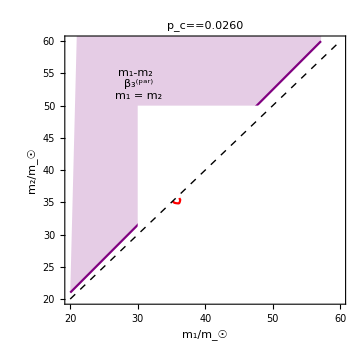

```mathematica
probability=prob;
(*probability=0.026;*)

(* 蓝色要对称一下 *)
PlotInversion[p,probability,20,60,1,cm->True,cd->True,cu->False,plotgr->False,projX->False,projY->False,funcName->IMRPhenomDBeta,spinPercentile1->0.5,spinPercentile2->0.5,contourIndices->{1,2}]
```

## Merger-RingDown

### alpha_2

```mathematica
(* ==========================================*)(*阶段一：预处理（算概率、提取红线）*)(* ==========================================*)
p="dalpha_2"; (*换参数改这里*)

m1Data=samples[p][[1]];
m2Data=samples[p][[2]];

(*算 PDF*)
m1m2[p]=Transpose[{m1Data,m2Data}];
(*{m1PriorRange[p],m2PriorRange[p]}=ChirpQRangeToMassRange[{10,80},{1,5}];*)
{m1PriorRange[p],m2PriorRange[p]}=ChirpQRangeToMassRange[{10,50}, {1, 3}];
m1m2PDF[p]=GetNormalizedPDF[m1m2[p],m1PriorRange[p],m2PriorRange[p]];

(*提取 0.005 密度对应的红线*)
contourPD[p]={0.01132};
{contourPlotObj[p],contourPoints[p]}=GetContourPlotAndPoints[m1m2PDF[p],m1PriorRange[p],m2PriorRange[p],contourPD[p]];
contourPoints[p][[1]]=SmoothContour[contourPoints[p][[1]]];

(*算出红线内部包含的真实后验概率 prob*)
prob=CalculateCredibleLevelsFromContours[m1m2PDF[p],{mergeSymmetricCurves[contourPoints[p][[1]],contourPoints[p][[2]],1]},"",False][[1]][[2]];

Print[p," 预处理完成，红线包含概率 prob = ",prob];
```

输入Mc范围：{10,50}

输入q范围：{1,3}

m1范围：{11.487,102.384}

m2范围：{6.82558,57.4349}

对称数据：原始 14828 + 镜像 14828

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1. and 6.11287×10^-6 for the integral and error estimates.

对称先验空间积分 = 1.（应接近1）

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1. and 6.11286×10^-6 for the integral and error estimates.

归一化验证 = 1.

Set::wrsym: Symbol Automatic is Protected.

对称边界框：{6.82558, 102.384} × {6.82558, 102.384}

等高线值：{0.01132}，共 2 条

第一条前3点：{{34.6142,34.3156},{34.6874,34.2447},{34.7063,34.2253}}

Set::setps: contourPoints[p] in the part assignment is not a symbol.

NIntegrate::regm: Method LocalAdaptive is not applicable for a region domain. Continuing with method Automatic.

=====  =====

包含片段数：1 (合并模式: False)

区域内总积分值：0.0967669

可信水平百分比：9.67669%

==========================

dalpha_2 预处理完成，红线包含概率 prob = 0.0967669

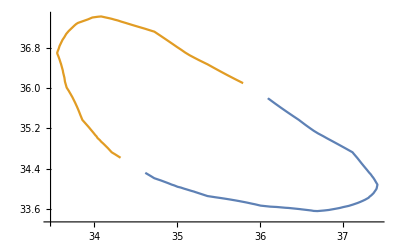

```mathematica
ListLinePlot[contourPoints[p]]
```

```mathematica
compPlots[p]=PlotComparisonBetween[samples[p][[7]],(*第7列：参数化系数样本*)samples[p][[6]],(*第6列：GR理论预测样本*)Range[10,100,1],(*m1 范围*)orderVal,(*阶数 order*)Median[chi1Data],(*自旋1*)Median[chi2Data]           (*自旋2*)]
```

```mathematica
prob
```

0.0967669

====== [dalpha_2] 反解校验报告 (容差: 1/100000) ======

实际使用的概率区间上下界: {0.451617, 0.548383}

实际使用的 GR 概率区间上下界: {-0.0677493, -0.0650892}

实际使用的 Param 概率区间上下界: {-0.0653594, -0.0616604}

Greater::nord: Invalid comparison with 26.4826+14.3067 ⅈ attempted.

Greater::nord: Invalid comparison with 26.5697+14.3558 ⅈ attempted.

Greater::nord: Invalid comparison with 26.6572+14.4042 ⅈ attempted.

General::stop: Further output of Greater::nord will be suppressed during this calculation.

GR下界: 点数=100 | Y>0点数=0 | 平均误差=0.0000893785

GR上界: 点数=100 | Y>0点数=100 | 平均误差=3.27516×10^-17

Param下界: 点数=100 | Y>0点数=100 | 平均误差=3.52496×10^-17

Param上界: 点数=100 | Y>0点数=100 | 平均误差=2.75474×10^-17

{{30.1,33.167},{30.2,33.2772},{30.3,33.3874},{30.4,33.4976},{30.5,33.6078}}

{{30.1,57.0122},{30.2,57.2016},{30.3,57.3911},{30.4,57.5805},{30.5,57.7699}}

chi1L取值：0.333189

chi2L取值：0.355229

=====================================================

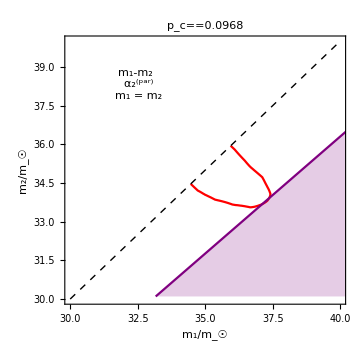

```mathematica
probability=prob;
(*probability=0.09676693194682148;*)

plots[p]=PlotInversion[p,probability,30,40,0.1,cm->True,cd->True,cu->True,plotgr->False,projX->False,projY->False,funcName->IMRPhenomDAlpha,spinPercentile1->0.5,spinPercentile2->0.5,contourIndices->{1,2},m1m2region->{mergeSymmetricCurves[contourPoints[p][[1]],contourPoints[p][[2]],1]}]
```

### alpha_3

```mathematica
(* ==========================================*)(*阶段一：预处理（算概率、提取红线）*)(* ==========================================*)
p="dalpha_3"; (*换参数改这里*)

m1Data=samples[p][[1]];
m2Data=samples[p][[2]];

(*算 PDF*)
m1m2[p]=Transpose[{m1Data,m2Data}];
{m1PriorRange[p],m2PriorRange[p]}=ChirpQRangeToMassRange[{10,60}, {1, 3}];
m1m2PDF[p]=GetNormalizedPDF[m1m2[p],m1PriorRange[p],m2PriorRange[p]];

(*提取 0.005 密度对应的红线*)
contourPD[p]={0.01108};
{contourPlotObj[p],contourPoints[p]}=GetContourPlotAndPoints[m1m2PDF[p],m1PriorRange[p],m2PriorRange[p],contourPD[p]];
contourPoints[p][[1]]=SmoothContour[contourPoints[p][[1]]];

(*算出红线内部包含的真实后验概率 prob*)
prob=CalculateCredibleLevelsFromContours[m1m2PDF[p],{mergeSymmetricCurves[contourPoints[p][[1]],contourPoints[p][[2]],0.8]},"",False][[1]][[2]];

Print[p," 预处理完成，红线包含概率 prob = ",prob];
```

=====  =====

包含片段数：1 (合并模式: False)

区域内总积分值：0.101437

可信水平百分比：10.1437%

==========================

dalpha_3 预处理完成，红线包含概率 prob = 0.101437

输入Mc范围：{10,60}

输入q范围：{1,3}

m1范围：{11.487,122.86}

m2范围：{6.82558,68.9219}

对称数据：原始 17962 + 镜像 17962

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1. and 4.69458×10^-6 for the integral and error estimates.

对称先验空间积分 = 1.（应接近1）

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1. and 4.69457×10^-6 for the integral and error estimates.

归一化验证 = 1.

Set::wrsym: Symbol Automatic is Protected.

对称边界框：{6.82558, 122.86} × {6.82558, 122.86}

等高线值：{0.01108}，共 2 条

第一条前3点：{{36.6073,36.2447},{36.6149,36.236},{36.7117,36.1276}}

Set::setps: contourPoints[p] in the part assignment is not a symbol.

NIntegrate::regm: Method LocalAdaptive is not applicable for a region domain. Continuing with method Automatic.

=====  =====

包含片段数：1 (合并模式: False)

区域内总积分值：0.101437

可信水平百分比：10.1437%

==========================

dalpha_3 预处理完成，红线包含概率 prob = 0.101437

归一化验证 = 1.

Set::wrsym: Symbol Automatic is Protected.

```mathematica
compPlots[p]=PlotComparisonBetween[samples[p][[7]],(*第7列：参数化系数样本*)samples[p][[6]],(*第6列：GR理论预测样本*)Range[10,100,1],(*m1 范围*)orderVal,(*阶数 order*)Median[chi1Data],(*自旋1*)Median[chi2Data]           (*自旋2*)]
```

```mathematica
prob
```

0.101437

====== [dalpha_3] 反解校验报告 (容差: 1/100000) ======

实际使用的概率区间上下界: {0.449281, 0.550719}

实际使用的 GR 概率区间上下界: {-24.7682, -22.4688}

实际使用的 Param 概率区间上下界: {-22.7615, -17.1703}

Greater::nord: Invalid comparison with 22.0533-6.87481 ⅈ attempted.

Greater::nord: Invalid comparison with 22.1452-6.9158 ⅈ attempted.

Greater::nord: Invalid comparison with 22.2385-6.95259 ⅈ attempted.

General::stop: Further output of Greater::nord will be suppressed during this calculation.

GR下界: 点数=270 | Y>0点数=0 | 平均误差=0.195646

GR上界: 点数=270 | Y>0点数=270 | 平均误差=3.7264×10^-14

Param下界: 点数=270 | Y>0点数=270 | 平均误差=3.5685×10^-14

Param上界: 点数=270 | Y>0点数=270 | 平均误差=3.5685×10^-14

{{23.1,26.6853},{23.2,26.8009},{23.3,26.9164},{23.4,27.0319},{23.5,27.1474}}

{{23.1,42.9965},{23.2,43.1826},{23.3,43.3687},{23.4,43.5549},{23.5,43.741}}

chi1L取值：0.306213

chi2L取值：0.385268

=====================================================

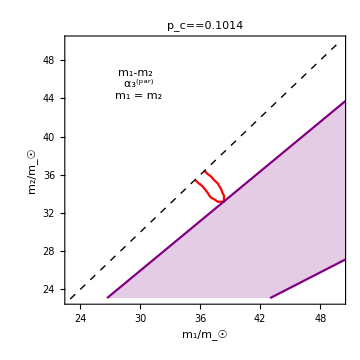

```mathematica
probability=prob;
(*probability=0.10143743087898953;*)

plots[p]=PlotInversion[p,probability,23,50,0.1,cm->True,cd->True,cu->True,plotgr->False,projX->False,projY->False,funcName->IMRPhenomDAlpha,spinPercentile1->0.5,spinPercentile2->0.5,contourIndices->{1,2},m1m2region->{mergeSymmetricCurves[contourPoints[p][[1]],contourPoints[p][[2]],2]}]
```

### alpha_4

```mathematica
(* ==========================================*)(*阶段一：预处理（算概率、提取红线）*)(* ==========================================*)
p="dalpha_4"; (*换参数改这里*)

m1Data=samples[p][[1]];
m2Data=samples[p][[2]];

(*算 PDF*)
m1m2[p]=Transpose[{m1Data,m2Data}];
{m1PriorRange[p],m2PriorRange[p]}=ChirpQRangeToMassRange[{15,45}, {1, 5}];
m1m2PDF[p]=GetNormalizedPDF[m1m2[p],m1PriorRange[p],m2PriorRange[p]];

(*提取 0.005 密度对应的红线*)
contourPD[p]={0.01532};
{contourPlotObj[p],contourPoints[p]}=GetContourPlotAndPoints[m1m2PDF[p],m1PriorRange[p],m2PriorRange[p],contourPD[p]];
contourPoints[p][[1]]=SmoothContour[contourPoints[p][[1]]];

(*算出红线内部包含的真实后验概率 prob*)
prob=CalculateCredibleLevelsFromContours[m1m2PDF[p],{mergeSymmetricCurves[contourPoints[p][[1]],contourPoints[p][[2]],0.8]},"",False][[1]][[2]];

Print[p," 预处理完成，红线包含概率 prob = ",prob];
```

输入Mc范围：{15,45}

输入q范围：{1,5}

m1范围：{17.2305,122.583}

m2范围：{8.17221,51.6914}

对称数据：原始 18402 + 镜像 18402

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1. and 2.57866×10^-6 for the integral and error estimates.

对称先验空间积分 = 1.（应接近1）

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1. and 2.57866×10^-6 for the integral and error estimates.

归一化验证 = 1.

Set::wrsym: Symbol Automatic is Protected.

对称边界框：{8.17221, 122.583} × {8.17221, 122.583}

等高线值：{0.01532}，共 2 条

第一条前3点：{{35.6431,35.2855},{35.6997,35.2416},{35.7191,35.2263}}

Set::setps: contourPoints[p] in the part assignment is not a symbol.

NIntegrate::regm: Method LocalAdaptive is not applicable for a region domain. Continuing with method Automatic.

=====  =====

包含片段数：1 (合并模式: False)

区域内总积分值：0.04027

可信水平百分比：4.027%

==========================

dalpha_4 预处理完成，红线包含概率 prob = 0.04027

```mathematica
compPlots[p]=PlotComparisonBetween[samples[p][[7]],(*第7列：参数化系数样本*)samples[p][[6]],(*第6列：GR理论预测样本*)Range[10,100,1],(*m1 范围*)orderVal,(*阶数 order*)Median[chi1Data],(*自旋1*)Median[chi2Data]           (*自旋2*)]
```

```mathematica
prob
```

0.04027

====== [dalpha_4] 反解校验报告 (容差: 1/100000) ======

实际使用的概率区间上下界: {0.479865, 0.520135}

实际使用的 GR 概率区间上下界: {0.26649, 0.266833}

实际使用的 Param 概率区间上下界: {0.260396, 0.26786}

GR下界: 点数=170 | Y>0点数=170 | 平均误差=5.25723×10^-17

GR上界: 点数=170 | Y>0点数=170 | 平均误差=4.27762×10^-17

Param下界: 点数=170 | Y>0点数=170 | 平均误差=4.5062×10^-17

Param上界: 点数=170 | Y>0点数=170 | 平均误差=4.96335×10^-17

{{28.1,39.648},{28.2,39.7891},{28.3,39.9302},{28.4,40.0713},{28.5,40.2124}}

{{28.1,30.6167},{28.2,30.7256},{28.3,30.8346},{28.4,30.9435},{28.5,31.0525}}

chi1L取值：0.379054

chi2L取值：0.370003

=====================================================

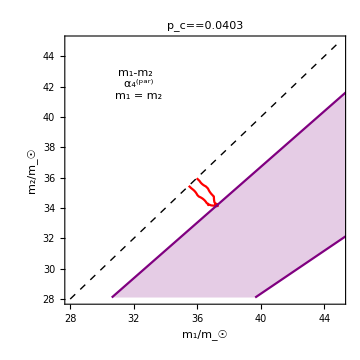

```mathematica
probability=prob;
(*probability=0.04026996258853606;*)

plots[p]=PlotInversion[p,probability,28,45,0.1,cm->True,cd->True,cu->True,plotgr->False,projX->False,projY->False,funcName->IMRPhenomDAlpha,spinPercentile1->0.5,spinPercentile2->0.5,contourIndices->{1,2},m1m2region->{mergeSymmetricCurves[contourPoints[p][[1]],contourPoints[p][[2]],2]}]
```

# Total plots

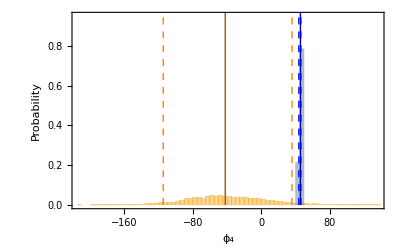

正在导出矢量图: plot_dphi_4_comp.pdf ...

正在导出矢量图: plot_dphi_7_comp.pdf ...

```mathematica
p="dphi_4"; 
compPlots[p]=PlotComparisonBetween[samples[p][[7]],(*第7列：参数化系数样本*)samples[p][[6]],Style["4",Italic]
,50
,Automatic
]
p="dphi_7"; 
compPlots[p]=PlotComparisonBetween[samples[p][[7]],(*第7列：参数化系数样本*)samples[p][[6]],Style["7",Italic]
,50
,Automatic
];
(*1. 定义你要存放 PDF 的文件夹名称*)
targetDir=FileNameJoin[{"D:\\Documents\\workspace\\课题\\论文\\fig\\","comp"}];

(*2. 如果目录不存在，则自动创建*)
If[!DirectoryQ[targetDir],CreateDirectory[targetDir];
Print["已自动创建目录: ",targetDir]];

Do[Print["正在导出矢量图: plot_",key,"_comp.pdf ..."];
Export[FileNameJoin[{targetDir,eventID<>"_"<>key<>"_comp.pdf"}],compPlots[key],"PDF",AllowRasterization->False (*强制全矢量输出，绝对高清*),ImageSize->500],
{key,Keys[compPlots]}]
```

```mathematica
(*1. 定义你要存放 PDF 的文件夹名称*)
targetDir=FileNameJoin[{"D:\\Documents\\workspace\\课题\\论文\\fig\\",eventID}];

(*2. 如果目录不存在，则自动创建*)
If[!DirectoryQ[targetDir],CreateDirectory[targetDir];
Print["已自动创建目录: ",targetDir]];

Do[Print["正在导出矢量图: plot_",key,".pdf ..."];
Export[FileNameJoin[{targetDir,eventID<>"_"<>key<>".pdf"}],plots[key],"PDF",AllowRasterization->False (*强制全矢量输出，绝对高清*),ImageSize->500],
{key,Keys[plots]}]
```

正在导出矢量图: plot_dphi_2.pdf ...

正在导出矢量图: plot_dphi_4.pdf ...

正在导出矢量图: plot_dphi_5l.pdf ...

正在导出矢量图: plot_dphi_6.pdf ...

正在导出矢量图: plot_dphi_7.pdf ...

正在导出矢量图: plot_dalpha_2.pdf ...

正在导出矢量图: plot_dalpha_3.pdf ...

正在导出矢量图: plot_dalpha_4.pdf ...